## Pregunta 1

### (1.a)

```mathematica
Clear[a0,an]
```

```mathematica
a0 = 1/Pi Integrate[Cos[t],{t,-Pi/2,Pi/2}]
```

2/π

```mathematica
an =Simplify[ 2/Pi Integrate[Cos[t]Cos[2 n t],{t,-Pi/2,Pi/2}],Element[n,Integers]]
```

(4 (-1)^n)/(π-4 n^2 π)

```mathematica
Clear[a0,an]
```

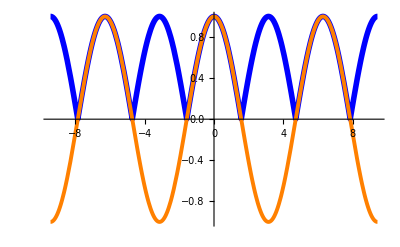

```mathematica
plot1a = Plot[2/Pi+ 4/Pi Sum[(-1)^(n+1)/(4 n^2-1)Cos[2 n t],{n,1,200}],{t,-3Pi,3Pi},PlotStyle->{Blue,Thickness[0.01]},PlotRange->All];
plot1b = Plot[Cos[t],{t,-3Pi,3Pi},PlotStyle->{Orange,Thickness[0.007]},PlotRange->All];
Show[plot1a,plot1b]
```

```mathematica
(*Si corresponder el coseno "rectidicado" *)
```

### (1.b)

```mathematica
Sum[(-1)^n/(4 n^2-1),{n,1,Infinity}]
```

(2-π)/4

### (1.c)

```mathematica
1/Pi Integrate[Cos[t]^2,{t,-Pi/2,Pi/2}]
```

1/2

```mathematica
Sum[1/((4 n^2-1)^2),{n,1,Infinity}]
```

1/16 (-8+π^2)

## Pregunta 2

```mathematica
Integrate[1/((a^2+w^2)^2),{w,-Infinity,Infinity}]
```

ConditionalExpression[1/2 (1/a^2)^(3/2) π,Re[a^2]≥0||a^2∉Reals]

## Pregunta 3

```mathematica
plot3a =Plot[-t*( UnitStep[t]-UnitStep[t-1]),{t,-3,3},PlotStyle->{Orange,Thickness[0.007]},PlotRange->All];
```

```mathematica
sumlimit=200;
```

```mathematica
plot3b =Plot[-1/4+Sum[((1-(-1)^n)/(2 n^2 Pi^2)-(I(-1)^n)/(2 n Pi))Exp[I n Pi t],{n,-sumlimit,-1}]+Sum[((1-(-1)^n)/(2 n^2 Pi^2)-(I(-1)^n)/(2 n Pi))Exp[I n Pi t],{n,1,sumlimit}],{t,-3,3},PlotStyle->{Blue,Thickness[0.01]},PlotRange->All];
```

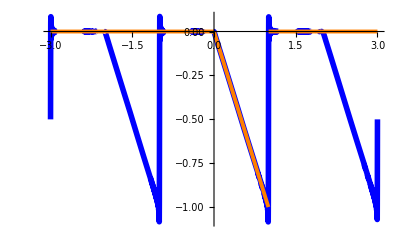

```mathematica
Show[plot3b,plot3a]
```

```mathematica
1/2 Integrate[(-t*( UnitStep[t]-UnitStep[t-1]))^2,{t,0,2}]
```

1/6

```mathematica
P=1/16+1/2 Abs[((1-(-1)^n)/(2 n^2 Pi^2)-(I(-1)^n)/(2 n Pi))]^2/.n->1
```

1/16+1/2 (1/π^4+1/(4 π^2))

```mathematica
N[P]
```

0.0802981

```mathematica
0.0802981/(1/6)
```

0.481789

## Pregunta 4

```mathematica
FourierTransform[Exp[-100 t]UnitStep[t],t,w,FourierParameters->{1, -1}]
```

-ⅈ/(-100 ⅈ+w)

```mathematica
Integrate[1/(100^2+w^2),{w,-Infinity,Infinity}]
```

π/100

```mathematica
Integrate[1/(100^2+w^2),{w,-wc,wc}]
```

ConditionalExpression[1/50 ArcTan[wc/100],Re[wc]≠0||-100<Im[wc]<0||0<Im[wc]<100]

## Pregunta 5

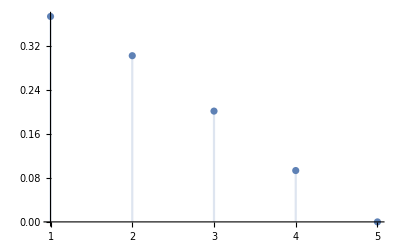

```mathematica
DiscretePlot[2/(n Pi)Sin[(n Pi)/5],{n,1,5}]
```

## Pregunta 6

```mathematica
InverseFourierTransform[Exp[- I w t0]-Exp[- I w t0] ( UnitStep[w+wc]-UnitStep[w-wc] ),w,t,FourierParameters->{1, -1}]
```

DiracDelta[-t+t0]+(ⅈ (-1+Cos[2 t wc-2 t0 wc]+ⅈ Sin[2 t wc-2 t0 wc]) (Cos[t wc-t0 wc]-ⅈ Sin[t wc-t0 wc]))/(2 π (t-t0))+ⅈ DiracDelta[t-t0] Sin[t wc-t0 wc]

```mathematica
Simplify[DiracDelta[-t+t0]+(ⅈ (-1+Cos[2 t wc-2 t0 wc]+ⅈ Sin[2 t wc-2 t0 wc]) (Cos[t wc-t0 wc]-ⅈ Sin[t wc-t0 wc]))/(2 π (t-t0))+ⅈ DiracDelta[t-t0] Sin[t wc-t0 wc],Element[{t,wc},Reals]]
```

DiracDelta[-t+t0]-Sin[(t-t0) wc]/(π t-π t0)+ⅈ DiracDelta[t-t0] Sin[(t-t0) wc]

```mathematica
(*Por alguna razon pone el termino DiracDelta[t-t0] Sin[(t-t0) wc], eso da 0 cuando se integra, peroo el resto si lo tenemos igual *)
```